## Woods-Saxon Potential

```mathematica
ClearAll["Global`*"]
```

Constants/Parameters

```mathematica
(*Constants (In Atomic Units)*)
m:=1
ℏ:=1
ke:=1    (*1/(4 π ϵ0)*)
e:=1
a0:=ℏ^2/(ke me e^2)    (*Units of length*)
Eh:=ℏ^2/(me a0^2)    (*Units of energy*)

(*Parameters*)
(*Mass number*)
A:=1
r0:=1    (*r0 = 1.25fm = 0.000028345891875*)
(*Surface Thickness of the Nucleus*)
a:= 1    (*a = 0.5fm = 1.889726125*10^-5*)
(*Nuclear Radius*)
R:=r0*A^(1/3)    (*R = r0*A^(1/3)*)
V0:=10    (*V0 = 50MeV = 1837466.10878*)

L:=10
T:=10
fps:=60
numstates:=8
```

Definitions

```mathematica
(*Potential Energy*)
V[x_]:=-V0/(1+Exp[(x-R)/a])

(*Time Independent Schrodinger Equation*)
H=-ℏ^2/(2 m) ψ''[x]+V[x]*ψ[x];
```

Energy Eigenvalues/Eigenfunctions

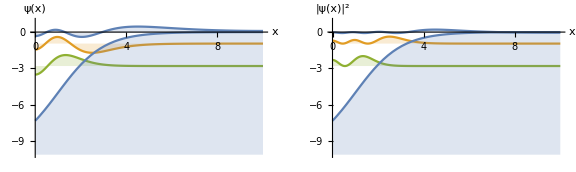

```mathematica
{vals,funs}=NDEigensystem[H,ψ[x],{x,0,L},numstates,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];

boundindices:=Flatten[Position[vals,_?(#<0&)]]
boundvals:=vals[[boundindices]]
boundfuns:=funs[[boundindices]]
numboundstates:=Length[boundvals]

lower:=-V0/(1+Exp[-R/a])+Min[boundvals]
upper:=Max[Map[FindMaxValue[{#,0<=x≤L},x]&,boundfuns]]
bounds:={lower,upper}

fillingrule:=Table[i->boundvals[[i]],{i,1,numboundstates}]
labels:=Table[ToString[Subscript[ψ, i],TraditionalForm],{i,1,numboundstates}]
title:=StringForm["Woods-Saxon Potential: First `` Bound Stationary States",numboundstates]

GraphicsRow[{Show[Plot[Evaluate[boundfuns+boundvals],{x,0,L},AxesLabel->{"x","ψ(x)"},Filling->fillingrule,PlotRange->bounds],Plot[V[x],{x,0,L},Filling->Bottom,PlotRange->bounds]],Show[Plot[Evaluate[boundfuns^2+boundvals],{x,0,L},AxesLabel->{"x","|ψ(x)|^2"},Filling->fillingrule,PlotRange->bounds],Plot[V[x],{x,0,L},Filling->Bottom,PlotRange->bounds]]},PlotLabel->title,ImageSize->Large]
```

Stationary States

```mathematica
ϵn[n_]:=Part[vals,n];
ψn[n_]:=Part[funs,n];
Ψn[n_]:=ψn[n] Exp[-ℏ ϵn[n] t/I];
```

Mixed State

```mathematica
ψ=ψn[1]+ψn[3]-ψn[4];
Ψ=Ψn[1]+Ψn[3]-Ψn[4];

norm=Sqrt[NIntegrate[(Conjugate[ψ] ψ),{x,0,L}]];
Ψ=Ψ/norm;
```

```mathematica
animation:=Animate[Show[Plot[Evaluate[Conjugate[Ψ] Ψ]/.t->s,{x,0,L},Axes->True,AxesLabel->{"x","|ψ(x)|^2"},PlotRange->{0,1},PlotStyle->Red],Plot[V[x],{x,0,L},Filling->Axis,PlotStyle->Black,Exclusions->None]],{s,0,T},DisplayAllSteps->True,DefaultDuration->T];
animation
```